```mathematica
Quit[];
```

#### Constants, pure Helium

```mathematica
X=0
Y=1
Z=2
A= 4
μa=Quantity["AtomicMassUnit"]/Quantity["gram"];
me=(Quantity["ElectronMass"]/Quantity["gram"]//UnitConvert); ee =(√(Quantity["ElementaryCharge"]^2/(4π Quantity["ElectricConstant"])))/(√((Quantity["g"] Quantity["cm"]^3)/Quantity["s"]^2))//UnitConvert;α=1/137;
hbar=Quantity["hbar"]/(Quantity["Erg"] Quantity["s"]); c = Quantity["SpeedOfLight"]/(Quantity["cm"]/Quantity["s"]);kB=Quantity["BoltzmannConstant"]/(Quantity["Erg"]/Quantity["Kelvin"]);σ=Quantity["StefanBoltzmannConstant"]/(Quantity["g"] Quantity["s"]^-3 Quantity["Kelvins"]^-4);
```

0

1

2

4

```mathematica
ni[ρ_]:=ρ/(A (Quantity[1,"ProtonMass"]/Quantity["gram"]//UnitConvert))
ne[ρ_]:=ni[ρ]/Z
```

### Timmes Opacity Fortran

#### Need Pressure of e+/- gas as input for Fotr an function

https://iopscience.iop.org/article/10.1086/313271/pdf

```mathematica
Block[{β,η,F,μ,sol,Pe,Pp},
β[T_]= (kB T)/(me c^2);
(*η[T_?NumericQ]:= μ/(kB T);*)
F[k_?NumericQ,η_?NumericQ, β_?NumericQ]:=NIntegrate[(x^k √(1+1/2 β x))/(Exp[x-η]+1),{x,0,10^10}] ;

Ne[T_?NumericQ,η_?NumericQ]:= (8π √2)/(hbar 2 π)^3 me^3 c^3  (β[T]^(3/2)  (F[1/2,η,β[T] ] + F[3/2,η,β[T] ] ));(*η is kinetic normalized chemical potential*)
Np[T_?NumericQ,η_?NumericQ]:= (8π √2)/(hbar 2 π)^3 me^3 c^3  (β[T]^(3/2)  (F[1/2,-(η+2/β[T]),β[T] ] + β[T] F[3/2,-(η+2/β[T]),β[T]] ));

Print[μ[10^6,10^3]];

Pe[T_,ρ_,η_] := (16π √2)/(3 (hbar 2π)^3)me^4 c^5 β[T]^(5/2)(F[3/2,η,β[T]]  + 1/2 β[T]  F[5/2,η,β[T]] );
Pp[T_,ρ_,η_] := (16π √2)/(3 (hbar 2π)^3)me^4 c^5 β[T]^(5/2)(F[3/2,-(η+2/β[T]),β[T]]  + 1/2 β[T]  F[5/2,-(η+2/β[T]),β[T]] );

Pep[T_,ρ_]:=Pe[T,ρ]+Pp[T,ρ];
sol[ρ_?NumericQ,T_?NumericQ]:=FindRoot[( ne[ρ]==  Ne[T,η]-Np[T,η]),{η,10^3}];
η/.sol[10^5,10^5]
(*Plot[η/.sol[ρ,10^6],{ρ,10^-10,10^10}(*,{T,10^-4,10^12}*)]*)
]
```

μ(1000000,1000)

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {η} = {1000.}. Try perturbing the initial point(s).

1000.

```mathematica
Block[{f},
f[n_?NumericQ]=NIntegrate[n,{x,0,2}];
NSolve[f[n]==2,n]
]
```

NIntegrate::inumr: The integrand n has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 2).

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{n→1.}}

### Other Opacity Formulas

0

1

2

4

```mathematica
{kcd@@#,kes@@#,kff@@#}^-1&@{10^3,6 10^1}//N
```

{1/(kcd(1000.,60.)),1/(kes(1000.,60.)),1/(kff(1000.,60.))}

Gotten from ....Iben??

```mathematica
kes[T_,ρ_] = 0.2 (1+X)
kff[T_,ρ_]= 41 ρ/((T/10^6)^(7/2))//N
krad[T_,ρ_]= (kes[T,ρ]^-1+ kff[T,ρ]^-1 )^-1
kcd[T_,ρ_]= (3.23 10^4 Z^2((T/10^6)^(1/2))/ρ)/(213 (ρ/10^6)^1/(μe (T/10^8)^(3/2)))/.μe-> 2
ktot[T_,ρ_]=(kcd[T,ρ]^-1+krad[T,ρ]^-1)^-1
```

0.2

(4.1×10^22 ρ)/T^(7/2)

1/((2.43902×10^-23 T^(7/2))/ρ+5.)

(1.21315×10^-6 T^2)/ρ^2

1/(5.+(2.43902×10^-23 T^(7/2))/ρ+(824303. ρ^2)/T^2)

```mathematica
LogLogPlot[{kes[T,10^4],kff[T,10^4],kff[T,10^4]+kes[T,10^4]},{T,10^4,10^9}]
```

-Graphics-

Combined Sources

```mathematica
Fkes[T_,ρ_] = 0.2 (1+X)
Fkff[T_,ρ_]=((Quantity["hbar"]^5 Quantity["c"]^2 Quantity["BoltzmannConstant"]^(-7/2)(Quantity["g cm^-3"] Quantity["Kelvin"]^(-7/2) Quantity["FineStructureConstant"]^3/(Quantity["ElectronMass"]^(3/2)Quantity["AtomicMassUnit"]^2)))/Quantity["cm^2 g^-1"]//UnitConvert )(2/(1+945 Zeta[7]/π^6))2/15 √((2π)/3)gauntff (1+X)(X+Y+B)ρ T^(-7/2)/.{gauntff-> 1,B->Z^2 X/A }(*Only works for Y=1 !!*) (*Fedderke et. al.*)

Fkrad[T_,ρ_]= (Fkes[T,ρ]+Fkff[T,ρ] )
Fkcd[T_,ρ_]= (3.23 10^4 Z^2((T/10^6)^(1/2))/ρ)/(213 (ρ/10^6)^1/(μe (T/10^8)^(3/2)))/.μe-> 2
Fktot[T_,ρ_]=(Fkcd[T,ρ]^-1+Fkrad[T,ρ]^-1)^-1
```

0.2

(3.7661×10^22 ρ)/T^(7/2)

(3.7661×10^22 ρ)/T^(7/2)+0.2

(1.21315×10^-6 T^2)/ρ^2

1/(1/((3.7661×10^22 ρ)/T^(7/2)+0.2)+(824303. ρ^2)/T^2)

```mathematica
ρtest=10^3;Ttest=6 10^6;
Numerical== 10^logκTρ[Log10@Ttest,Log10@ρtest]
Analytic== ktot[Ttest,ρtest]
Subscript[k, rad]== Fkrad[Ttest,ρtest]
Subscript[k, es]==  Fkes[Ttest,ρtest]
Subscript[k, ff]== Fkff[Ttest,ρtest]
Fkcd[Ttest,ρtest]
```

Numerical==10^(logκTρ((log(6000000))/(log(10)),3))

Analytic==ktot(6000000,1000)

k_rad==71.3799

k_es==0.2

k_ff==71.18

43.6732

```mathematica
Log10@ktot=-Log10@(kcd^-1+krad^-1)
```

Gotten from IOP-516819- “Updated Electron-Conduction Opacitites The Impact” : Cassisi Potekhin Pietrinkferni Catelan Salaris 2007

```mathematica
Quantity["hbar"]/(Quantity["Erg"] Quantity["s"])
```

1.054572×10^-27

```mathematica
(α hbar c ((4π)/3 ne)^(1/3))/(kB T)/.T-> T6 10^6/.ne-> ρ/μa
```

(0.22753 ρ^(1/3))/T6

```mathematica
(*TF[ρ_]:=5.93 10^9(√(1+(xr)^2) - 1)/.xr-> 0.01009(ρ Zi / A)^(1/3) (*TF in Kelvin, ρ in g/cm^3*) (*Is relativistic, but looks like holds for nonrel*)*)




Nkcd[ρ_?NumericQ,T_?NumericQ]:=Module[{a,χkinetic,ν,xr,pF,vF,βr,γr,y,Ir,νee,νeeDegen,Λei,Λee,νei,kcd,ktot},
TF:=5.93 10^9(√(1+(xr)^2) - 1); (*TF in Kelvin, ρ in g/cm^3*) (*Is relativistic, but looks like holds for nonrel*)
xr= 0.01009(ρ Z/ A)^(1/3);
pF=me c  xr;
 γr=√(1+xr^2);
vF=pF/(me γr);
βr=vF/c;
y=571.6/(T/10^6)βr^(1/2)xr;
a:= Piecewise[{{3/2,T≥ TF},{π^2/3,T<TF}}];

Λee:= Log[rmax/rmin]/.{rmax-> √((kB T)/(4π ne[ρ] ee^2)),rmin-> Max[√((2π hbar^2)/(me kB T)),ee^2/(kB T)]}; (*Same as above, but adjusted for electron-electron by me*)
νee:= 8/3 √(π/me)ee^4/(kB T)^(3/2)ne[ρ] Λee;
ΛeiCassissiNDNR:= Log[rmax/rmin]/.{rmax-> √((kB T)/(4π (ne[ρ] + Z^2 ni[ρ])ee^2)),rmin-> Max[√((2π hbar^2)/(me kB T)),(Z ee^2)/(kB T)]};

νeiCassissiNDNR:= 4/3 √((2π)/me)(Z^2 ee^4)/(kB T)^(3/2)ni[ρ] ΛeiCassissiNDNR ;

ΛeiCassissiDNRLargeΓ:= Log[rmax/rmin]/.{rmax-> √((kB T)/(4π (ne[ρ] + Z^2 ni[ρ])ee^2)),rmin-> Max[√((2π hbar^2)/(me kB T)),(Z ee^2)/(kB T)]};(* Γ>1 precisely *)

νeiCassissiDNRLargeΓ:= (4π)/(pF^2 vF)(Z^2 ee^4)/(kB T)^(3/2)ni[ρ] ΛeiDNRLargeΓ;

ΛeiMonteroCamacho:= Log[(2/3 π Z)^(1/3)(3/2+3/Γe)^(1/2) - x^2/(2(1+x^2))]/.{x-> xr, Γe -> (α hbar c ((4π)/3 ne[ρ])^(1/3))/(kB T) (*dimensionless plasma coupling*)};(*Need to check this x is same as xr, and γr right*)

νeiMonteroCamacho:= (4 α^2 c^2)/(3π hbar) Z ΛeiMonteroCamacho (me γr);


Ir=1/βr(10/63-(8/315)/(1+0.0435 y)) Log[1+128.56/(37.1y+10.83 y^2+y^3)]+βr^3(2.404/cB+ (cC-2.404/cB)/(1+0.1 βr y)) Log[1+cB/(cA βr y + (βr y)^2)] + βr/(1+cD)(cC + (18.52 βr^2 cD)/cB)Log[1+cB/(cA y + 10.83 (βr y)^2 +(βr y)^(8/3))]//. {cA->12.2 + 25.2 βr^3 ,cB->cA Exp[(0.123636 + 0.016234 βr^2)/cC] ,cC->8/105+0.05714 βr^4 ,cD->0.1558 y^(1-0.75 βr) };

νeeDegen= ((me c^2)/hbar (6 α^(3/2))/π^(5/2)xr y √βr Ir)(*(1+t^2)/(1+t+b t^2 √(T/TF))/.{t-> 25 T/TF,b-> 0.434}*);
ν= νei+νeeDegen (*Only exactly right for completely degenrate electrons!*);
χkinetic:= (a ne[ρ] kB^2 T)/(me γr ν);(*The thermal conductivity, degenerate region of a agrees with Montero-Camacho 2019 (up to what ν is)*)
kcd=(16 σ T^3)/(3 ρ χkinetic);
Print["veeDegen is: ", νeeDegen];
Print["TF, xr are: ", TF, "  ", xr];
kcd
]
ρTest=2 10^4; 
Ttest=10^4;

Nkcd[Ttest,ρTest]
(*Fkcd[Ttest,ρTest]
LogLogPlot[{Nkcd[T,10^4],Fkcd[T,10^4]},{T,10^4,10^10}]*)
```

veeDegen is: 3.02021×10^12

TF, xr are: 8.76174×10^7  0.172537

2.38601×10^-22 (νei$706986+3.02021×10^12)

```mathematica
(1.0+6.0/(5.0*xrel^2)+2.0/(5.0*xrel^4))*(yg^3/(3.0*(1.0+0.07414*yg)^3)*Log[(2.81^9-0.810*beta2+yg)/yg]+π^5/6.0*(yg/13.91+yg))^4//.{yg-> rt3*tpe/temp,tpe-> xec*√(xne/ymas),rt3-> 1.7320508075688772,temp-> T,xec-> 4.309054377592449  10^-7,xne-> ne,ymas-> √(1.0+xmas^2),xmas-> meff*ne^(1/3),meff-> 1.19464864240144  10^-10}//Simplify

vee=0.511 T^2*xmas/ymas^2 √(xmas/ymas)%//.{yg-> rt3*tpe/temp,tpe-> xec*√(xne/ymas),rt3-> 1.7320508075688772,temp-> T,xec-> 4.309054377592449  10^-7,xne-> ne,ymas-> √(1.0+xmas^2),xmas-> meff*ne^(1/3),meff-> 1.19464864240144  10^-10,beta2-> xrel^2/(1.0+xrel^2)}//Simplify
vee/.{ne-> ne[ρ],xrel-> 0.01009(ρ Z/ A)^(1/3)}/.{T->Ttest,ρ-> ρTest}//N
```

(1. ne^2 (1.+0.4/xrel^4+1.2/xrel^2) ((1.38582×10^-19 ne T log(((1.46357×10^10-1.08528×10^6 beta2) T)/(√(ne/(√(1.42719×10^-20 ne^(2/3)+1.))))+1.))/(√(1.42719×10^-20 ne^(2/3)+1.) (5.53344×10^-8 √(ne/(√(1.42719×10^-20 ne^(2/3)+1.)))+1. T)^3)+0.0000408029)^4)/((1.42719×10^-20 ne^(2/3)+1.) T^4)

(6.67239×10^-16 √(ne^(1/3)/(√(1.42719×10^-20 ne^(2/3)+1.))) ne^(7/3) (1.+0.4/xrel^4+1.2/xrel^2) ((1.38582×10^-19 ne T log((T (1.46357×10^10-(1.08528×10^6 xrel^2)/(xrel^2+1.)))/(√(ne/(√(1.42719×10^-20 ne^(2/3)+1.))))+1.))/(√(1.42719×10^-20 ne^(2/3)+1.) (5.53344×10^-8 √(ne/(√(1.42719×10^-20 ne^(2/3)+1.)))+1. T)^3)+0.0000408029)^4)/((1.42719×10^-20 ne^(2/3)+1.)^2 T^2)

3.25194×10^29

```mathematica
(4π)/(pF^2 vF)Z^2 ee^4 ni[ρ] Λei//.{pF-> me c  xr,vF->pF/(me γr)}
(4 α^2 c^2)/(3π hbar) Z Λei (me γr)
```

(1.78853×10^10 γr Λei ρ)/xr^3

3.511009×10^16 γr Λei

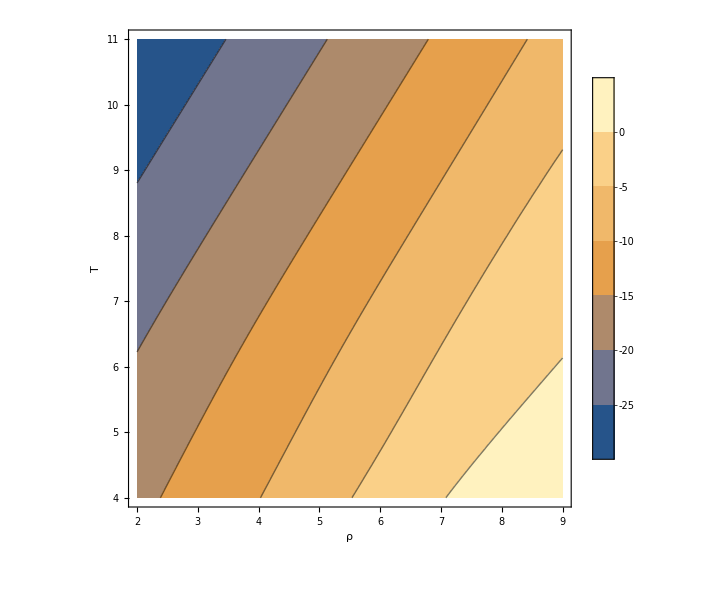
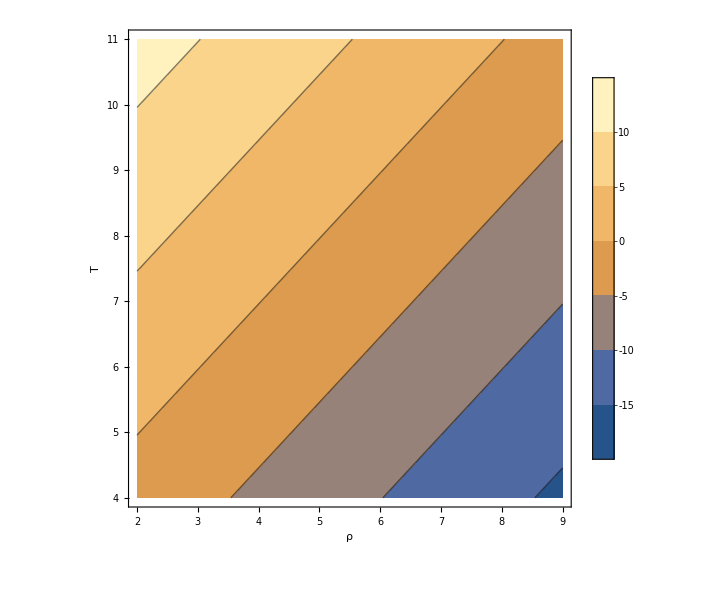

```mathematica
{ContourPlot[Log10@Nkcd[T,ρ],{ρ,10^2,10^9},{T,10^4,10^11},ScalingFunctions->{"Log10","Log10"},ImageSize->600,Frame-> True,FrameLabel-> {{"T",""},{"ρ","Log10@R"}},FrameStyle->Directive[FontSize-> 20],Contours-> Automatic,PlotLegends->Automatic],
ContourPlot[Log10@Fkcd[T,ρ],{ρ,10^2,10^9},{T,10^4,10^11},ScalingFunctions->{"Log10","Log10"},ImageSize->600,Frame-> True,FrameLabel-> {{"T",""},{"ρ","Log10@R"}},FrameStyle->Directive[FontSize-> 20],Contours-> Automatic,PlotLegends->Automatic]}
```

## Numerical Tables from https://opalopacity.llnl.gov/existing.html#type1GN

#### Region where Opacity tables typically work

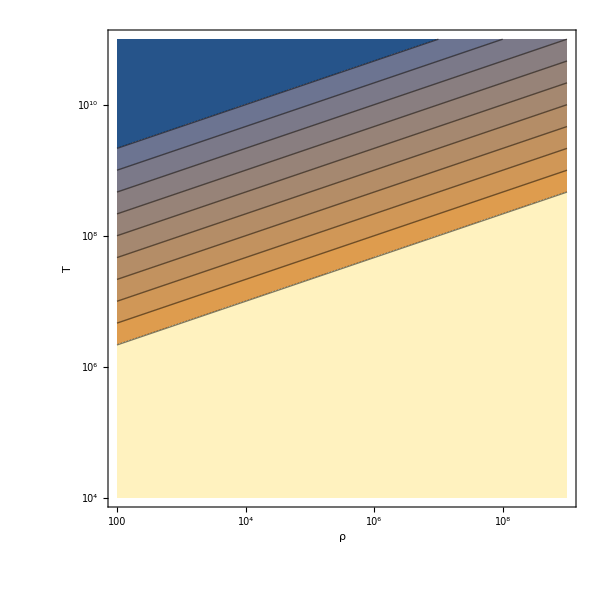

```mathematica
ContourPlot[Log10@ρ-3 Log10@T + 18,{ρ,10^2,10^9},{T,10^4,10^11},ScalingFunctions->{"Log10","Log10"},ImageSize->600,Frame-> True,FrameLabel-> {{"T",""},{"ρ","Log10@R"}},FrameStyle->Directive[FontSize-> 20],Contours-> Range[-8,1]]
```

#### Checks on numerical vs analytic

Keeping only square part of data set for now, involves removing last 13 lines
logs are log10, T6=T/10^6K, or Log10@T6=Log10@T - 6
R== ρ/T6^3 
logR== logρ- 3 log T6== logρ-3 ( log10 - 6)

```mathematica
rawκdata=Import["/home/zach/Research/Other_Projects/Helium_Flash/Opacity-Type1_x0y1z0.txt","Table","FieldSeparators"-> " "];
Tdata=rawκdata[[5;;-14,1]]
Rdata=rawκdata[[3,2;;]]
logκdata=rawκdata[[5;;-14 ,2;;]];
shortκtable=Table[{{Tdata[[i]],Rdata[[j]]},logκdata[[i,j]]},{i,1,Length@Tdata},{j,1,Length@Rdata}]//Flatten[#,1]&;
```

{3.75,3.8,3.85,3.9,3.95,4.,4.05,4.1,4.15,4.2,4.25,4.3,4.35,4.4,4.45,4.5,4.55,4.6,4.65,4.7,4.75,4.8,4.85,4.9,4.95,5.,5.05,5.1,5.15,5.2,5.25,5.3,5.35,5.4,5.45,5.5,5.55,5.6,5.65,5.7,5.75,5.8,5.85,5.9,5.95,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1}

{-8.,-7.5,-7.,-6.5,-6.,-5.5,-5.,-4.5,-4.,-3.5,-3.,-2.5,-2.,-1.5,-1.,-0.5,0.,0.5,1.}

```mathematica
logκTR[logT_,logR_]:=Interpolation[shortκtable][logT,logR]
logκTρ[logT_,logρ_]:=logκTR[logT,logρ -3 (logT-6) ]
```

```mathematica
logκTρ[5,1 +3 (5-6)]
```

4.752

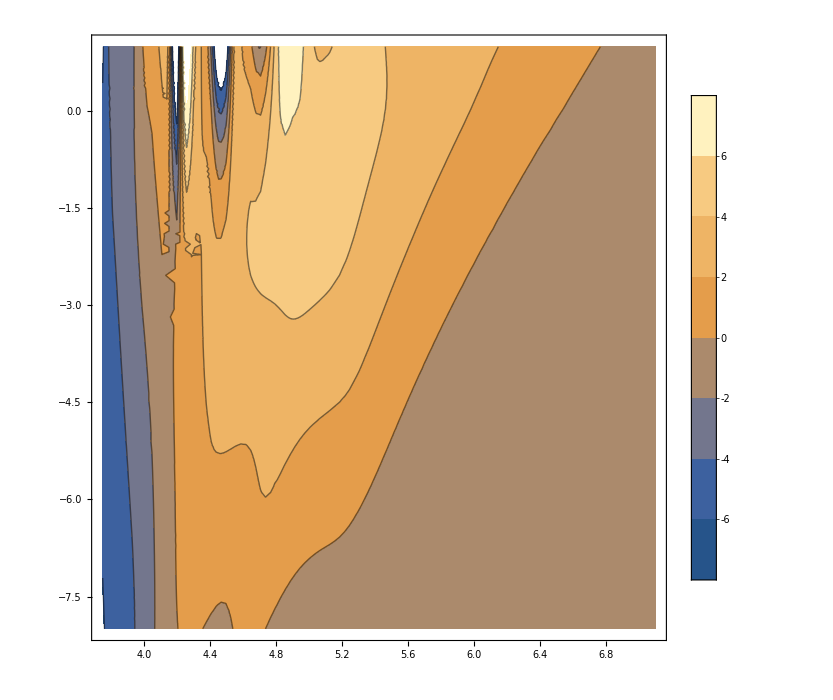

```mathematica
ContourPlot[logκTρ[logT,logR],{logT,3.75,7.1},{logR,-8,1},ImageSize->700,PlotLegends->Automatic]
```

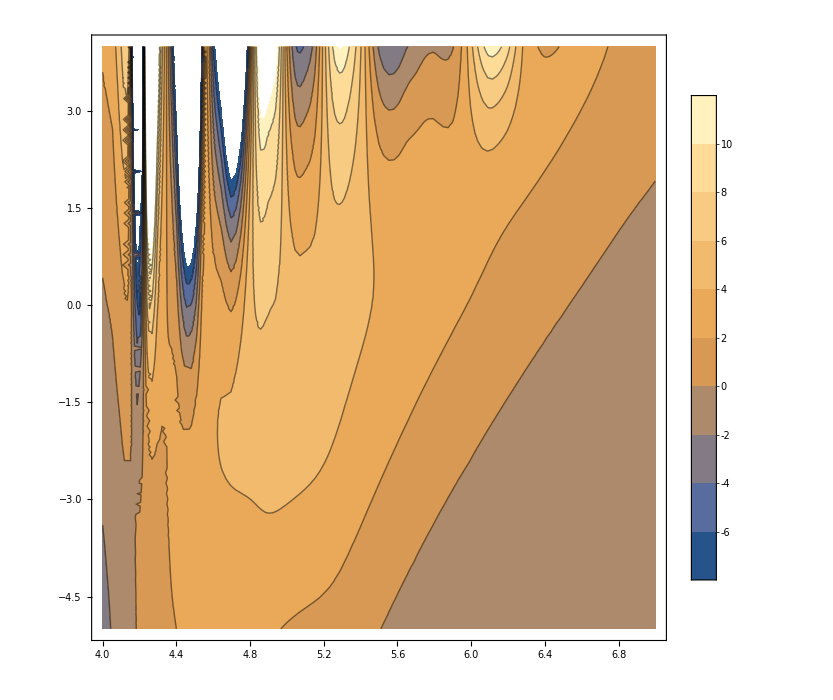

```mathematica
ContourPlot[logκTρ[logT,logρ],{logT,4,7},{logρ,-5,4},ImageSize->700,PlotLegends->Automatic]
```

## Plot Section

```mathematica
ne[1009]
```

7.540557×10^25

```mathematica
TimmesData={{1009,6448231},
{3178,11794467},
{16030,29176619},
{50499,57841262},
{278233,148962490},
{1045722,346904386},
{2182053,450657034},
{6110740,745379806},
{7508264,775997174},
{23652659,1363375184},
{95682620,2813848425}}
```

(1009 | 6448231
3178 | 11794467
16030 | 29176619
50499 | 57841262
278233 | 148962490
1045722 | 346904386
2182053 | 450657034
6110740 | 745379806
7508264 | 775997174
23652659 | 1363375184
95682620 | 2813848425)

ReplaceAll::reps: {NSolve[{Nkcd(T,100.033)==0.2+(3.7673×10^24)/T^(7/2),T>0},T]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NSolve[{Nkcd(T,100.033)==0.2+(3.7673×10^24)/T^(7/2),T>0.},T]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {NSolve[{Nkcd(T,138.995)==0.2+(5.23464×10^24)/T^(7/2),T>0},T]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

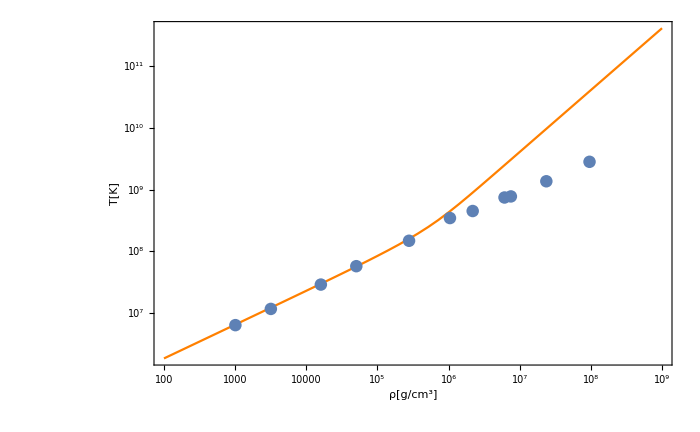

```mathematica
Tstar[ρ_?NumericQ]:=NSolve[{Fkcd[T,ρ]==Fkrad[T,ρ],T>0},T]
Tstar2[ρ_?NumericQ]:=NSolve[{Evaluate@Nkcd[T,ρ]==Fkrad[T,ρ],T>0},T]
Show[
LogLogPlot[{T/.Tstar[ρ],T/.Tstar2[ρ]},{ρ,10^2,10^9},ImageSize->700,GridLines->Automatic,Frame-> True,FrameStyle->Directive[FontSize-> 20],PlotStyle->Orange,FrameLabel->{"ρ[g/cm^3]","T[K]"}]
,ListLogLogPlot[TimmesData]
]
```

For all cases, for U kinetic enrgy density per volume, U=3/2 P, however what P is is strongly dependent on whether electrons are degenerate, etc.
Timmes uses  E=U/ρ

```mathematica
TcritEstimate=3 10^8
c= 3 10^10; MH = Quantity["AtomicMassUnit"]/Quantity["g"](*really hydrogen mass but whatever*);μe=2 ;k=(Quantity["BoltzmannConstant"]/(Quantity["g cm^2"]/Quantity["s^2"]/Quantity["Kelvin"]))//UnitConvert//Simplify



(*ENRnonD[ρ_,T_]:= 3/2(1/μe ρ/MH k T)/ρ
ENRweakD[ρ_,T_]:= 3/2
ENRstrongD[ρ_,T_]:= 3/2(0.990647 10^13)1/ρ (ρ/(μe MH))^(5/3) (*In dynes/gram*)
ENRintD[ρ_,T_]:= 3/2
WT[ρ_,T_]:= √((c ENRnonD[ρ,T])/(Fktot[T,ρ]S3alpha[ρ,T]))*)
WT2[ρ_,T_]:= √(1.03344 10^7 T^4/(Fktot[T,ρ] ρ^2 S3alpha[ρ,T])) (*rederived by me, but from Fedderke et. al.*)
WT3[ρ_,T_]:= √(1.03344 10^7 T^4/(10^logκTρ[T,ρ] ρ^2 S3alpha[ρ,T])) (*rederived by me, but from Fedderke et. al.*)
MT[ρ_,T_]:= 4/3 π WT2[ρ,T]^3 ρ

S3alpha[ρ_,T_]=5.1 10^8 ρ^2(1/(T/10^9))^3 E^(-4.4027/(T/10^9))
```

300000000

1.38065×10^-16

(5.1×10^35 ρ^2 ⅇ^(-4.4027×10^9/T))/T^3

Keep the crap below because it is origin of 1.03344 10^7 unit conversion in tirgger length calculation

```mathematica
(Quantity["BoltzmannConstant"]^4/(Quantity["hbar"]^3 Quantity["c"]))/(Quantity["erg"]/(Quantity["Kelvin"]^4 Quantity["s"]^2 Quantity["cm"]))
```

1.0334×10^7

```mathematica
Timmes2000DataLine1={{0.146,1.26   10^24},{0.150,4.63   10^23},{0.156,1.53   10^23},{0.160,5.79   10^22},{0.164,2.16   10^22},{0.169,8.34   10^21},{0.175,3.06   10^21},{0.182,1.04   10^21},{0.188,3.73   10^20},{0.196,1.34   10^20},{0.205,4.47   10^19},{0.216,1.65   10^19},{0.224,6.61   10^18},{0.234,2.60   10^18},{0.246,9.41   10^17},{0.259,3.60   10^17},{0.273,1.46   10^17},{0.289,6.07   10^16},{0.307,2.52   10^16},{0.328,1.02   10^16},{0.353,4.34   10^15},{0.379,2.06   10^15},{0.405,1.15   10^15},{0.431,6.89   10^14},{0.458,4.61   10^14},{0.484,3.25   10^14},{0.510,2.47   10^14},{0.536,1.98   10^14},{0.563,1.65   10^14},{0.589,1.45   10^14},{0.615,1.30   10^14},{0.641,1.20   10^14},{0.667,1.18   10^14},{0.692,1.15   10^14},{0.720,1.17   10^14},{0.746,1.18   10^14},{0.772,1.18   10^14},{0.798,1.23   10^14},{0.825,1.30   10^14},{0.851,1.39   10^14},{0.877,1.51   10^14},{0.903,1.65   10^14},{0.929,1.83   10^14},{0.956,1.98   10^14},{0.982,2.21   10^14},{1.01,2.49   10^14},{1.03,2.77   10^14},{1.06,3.11   10^14},{1.09,3.52   10^14},{1.11,3.98   10^14},{1.14,4.60   10^14},{1.17,5.23   10^14},{1.19,5.94   10^14},{1.22,6.84   10^14},{1.24,7.75   10^14},{1.27,8.94   10^14},{1.30,1.03   10^15},{1.32,1.15   10^15},{1.35,1.33   10^15},{1.37,1.53   10^15},{1.40,1.72   10^15},{1.43,1.94   10^15},{1.48,2.46   10^15},{0.141,8.02   10^24}}//Sort;

Timmes2000DataLine2={{0.138,7.32   10^22},{0.142,2.40   10^22},{0.147,5.30   10^21},{0.159,2.66   10^20},{0.165,7.44   10^19},{0.170,2.90   10^19},{0.197,2.61   10^17},{0.204,9.64   10^16},{0.211,3.95   10^16},{0.220,1.64   10^16},{0.229,6.42   10^15},{0.238,2.72   10^15},{0.249,1.11   10^15},{0.260,4.54   10^14},{0.273,1.94   10^14},{0.287,8.13   10^13},{0.302,3.38   10^13},{0.320,1.41   10^13},{0.342,5.96   10^12},{0.366,2.55   10^12},{0.393,1.20   10^12},{0.419,6.30   10^11},{0.445,3.59   10^11},{0.471,2.30   10^11},{0.497,1.57   10^11},{0.524,1.16   10^11},{0.550,8.90   10^10},{0.576,7.06   10^10},{0.602,5.77   10^10},{0.629,4.87   10^10},{0.655,4.25   10^10},{0.681,3.75   10^10},{0.707,3.51   10^10},{0.733,3.16   10^10},{0.760,3.04   10^10},{0.786,2.89   10^10},{0.812,2.83   10^10},{0.838,2.74   10^10},{0.864,2.70   10^10},{0.891,2.67   10^10},{0.917,2.72   10^10},{0.943,2.73   10^10},{0.969,2.83   10^10},{0.995,2.83   10^10},{1.02,2.98   10^10},{1.05,3.07   10^10},{1.07,3.11   10^10},{1.10,3.33   10^10},{1.13,3.51   10^10},{1.15,3.65   10^10},{1.18,3.85   10^10},{1.21,4.09   10^10},{1.23,4.32   10^10},{1.26,4.65   10^10},{1.28,4.96   10^10},{1.31,5.36   10^10},{1.34,5.72   10^10},{1.36,6.20   10^10},{1.39,6.55   10^10},{1.41,7.07   10^10},{1.44,7.66   10^10},{1.47,8.62   10^10},{1.49,9.14   10^10},{0.126,7.51   10^24},{0.179,6.34   10^18}}//Sort;

Timmes2000DataLine3={{0.124,3.41   10^24},{0.131,3.46   10^23},{0.158,6.88   10^19},{0.177,1.15   10^18},{0.193,6.64   10^16},{0.199,2.57   10^16},{0.205,1.01   10^16},{0.212,3.52   10^15},{0.221,1.29   10^15},{0.229,4.54   10^14},{0.239,1.65   10^14},{0.248,6.66   10^13},{0.258,2.78   10^13},{0.269,1.14   10^13},{0.281,4.49   10^12},{0.294,1.80   10^12},{0.309,7.02   10^11},{0.326,2.74   10^11},{0.345,1.14   10^11},{0.366,4.74   10^10},{0.389,2.05   10^10},{0.414,9.24   10^9},{0.440,4.63   10^9},{0.467,2.56   10^9},{0.493,1.49   10^9},{0.519,9.54   10^8},{0.545,6.51   10^8},{0.571,4.64   10^8},{0.598,3.49   10^8},{0.624,2.72   10^8},{0.650,2.20   10^8},{0.676,1.85   10^8},{0.703,1.57   10^8},{0.729,1.33   10^8},{0.755,1.15   10^8},{0.781,1.03   10^8},{0.807,9.18   10^7},{0.834,8.39   10^7},{0.860,7.64   10^7},{0.886,7.09   10^7},{0.912,6.65   10^7},{0.938,6.19   10^7},{0.965,5.84   10^7},{0.991,5.68   10^7},{1.02,5.41   10^7},{1.04,5.26   10^7},{1.07,5.05   10^7},{1.10,4.88   10^7},{1.12,4.82   10^7},{1.15,4.82   10^7},{1.17,4.81   10^7},{1.20,4.82   10^7},{1.23,4.80   10^7},{1.25,4.82   10^7},{1.28,4.82   10^7},{1.31,4.82   10^7},{1.33,4.82   10^7},{1.36,4.82   10^7},{1.38,4.86   10^7},{1.41,4.98   10^7},{1.44,5.51   10^7},{1.46,5.91   10^7},{1.49,6.05   10^7},{0.144,4.24   10^21},{0.122,9.13   10^24}}//Sort;

Timmes2000DataLine4={{0.111,1.82   10^24},{0.121,2.82   10^22},{0.127,4.42   10^21},{0.137,2.26   10^20},{0.143,3.69   10^19},{0.151,5.81   10^18},{0.160,7.55   10^17},{0.170,8.84   10^16},{0.176,3.10   10^16},{0.182,1.22   10^16},{0.187,4.43   10^15},{0.194,1.71   10^15},{0.201,6.60   10^14},{0.208,2.51   10^14},{0.219,8.91   10^13},{0.229,2.73   10^13},{0.238,1.13   10^13},{0.249,4.31   10^12},{0.260,1.85   10^12},{0.271,7.59   10^11},{0.284,3.01   10^11},{0.298,1.21   10^11},{0.312,4.97   10^10},{0.330,2.03   10^10},{0.349,8.08   10^9},{0.371,3.22   10^9},{0.396,1.28   10^9},{0.422,5.64   10^8},{0.449,2.79   10^8},{0.475,1.55   10^8},{0.501,8.63   10^7},{0.527,5.10   10^7},{0.554,3.17   10^7},{0.580,2.11   10^7},{0.606,1.47   10^7},{0.632,1.06   10^7},{0.659,8.09   10^6},{0.685,6.35   10^6},{0.716,4.76   10^6},{0.742,3.87   10^6},{0.768,3.20   10^6},{0.795,2.68   10^6},{0.821,2.29   10^6},{0.847,1.98   10^6},{0.873,1.76   10^6},{0.899,1.54   10^6},{0.926,1.38   10^6},{0.952,1.26   10^6},{0.978,1.14   10^6},{1.00,1.04   10^6},{1.03,9.61   10^5},{1.06,8.81   10^5},{1.08,8.55   10^5},{1.11,8.06   10^5},{1.14,7.49   10^5},{1.16,7.24   10^5},{1.19,6.88   10^5},{1.21,6.72   10^5},{1.24,6.37   10^5},{1.27,6.34   10^5},{1.29,6.04   10^5},{1.32,5.84   10^5},{1.34,5.84   10^5},{1.37,5.84   10^5},{1.40,5.84   10^5},{1.42,5.84   10^5},{1.44,5.84   10^5},{0.117,2.24   10^23},{0.107,8.55   10^24}}//Sort;
```

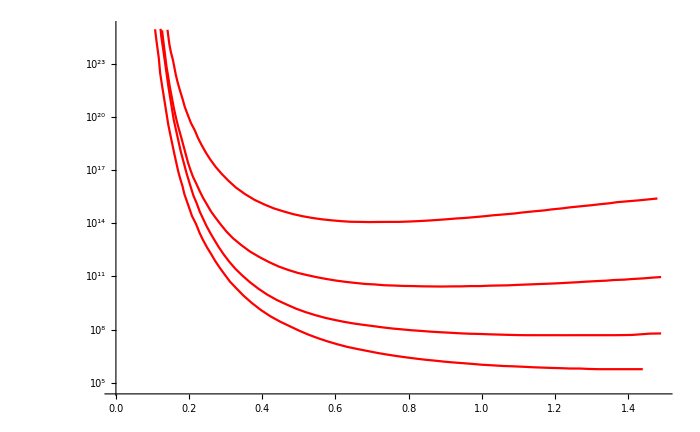

1.92667×10^-18

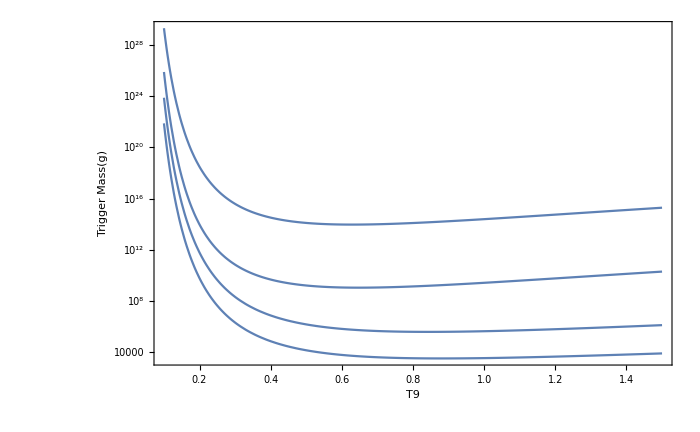

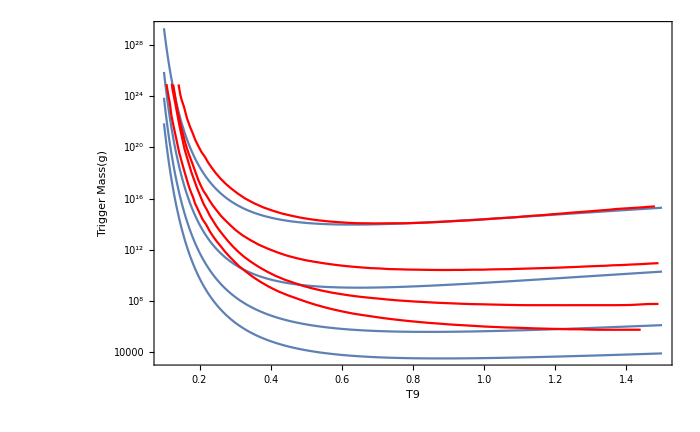

```mathematica
TimmesTriggerMassPlot=ListLogPlot[{Timmes2000DataLine1,Timmes2000DataLine2,Timmes2000DataLine3,Timmes2000DataLine4},Joined->True,PlotStyle->Red(*,PlotRange->{{0.7,0.71},{10^5,10^15}}*),ImageSize->700,GridLines->Automatic]
rescaling = (1.23   10^14)/MT[6 10^4, 0.798 10^9]
(*ZCTriggerMassPlot=LogPlot[rescaling{MT[6 10^4,T9 10^9]},{T9,.1,1.5},ImageSize->700,Frame-> True,FrameStyle->Directive[FontSize-> 20],PlotLegends->"Expressions",FrameLabel->{"T9","Trigger Mass(g)"}]*)
ZCTriggerMassPlot=LogPlot[rescaling{MT[6 10^4,T9 10^9],MT[6 10^5,T9 10^9],MT[6 10^6,T9 10^9],MT[6 10^7,T9 10^9]},{T9,.1,1.5},ImageSize->700,Frame-> True,FrameStyle->Directive[FontSize-> 20],PlotLegends->"Expressions",FrameLabel->{"T9","Trigger Mass(g)"}]
Show[{ZCTriggerMassPlot,TimmesTriggerMassPlot}]
```

```mathematica
v  =Quantity[{1,10^4},"cm s^-1"]
(*v  =Quantity[2,"cm s^-1"]*)
circ= Quantity[2 π 0.1, "SolarRadius"]

τ== ((circ/v )//UnitConvert[#,"years"]&)
```

{1 cm/s,10000 cm/s}

0.628319 ℛ_☉^N

τ=={1386.1 yr,0.13861 yr}